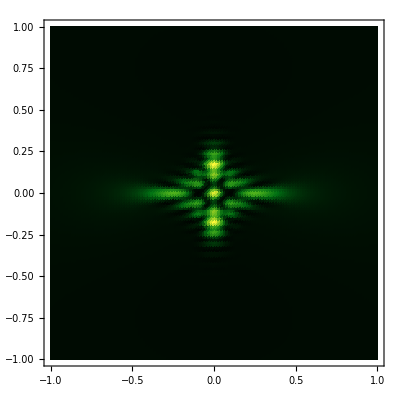

```mathematica
SetDirectory[NotebookDirectory[]];
ν=100;
data=ν/(2π ⅈ)Module[{dataR=Partition[BinaryReadList["result.bin","Real64"],2].{1,ⅈ}},Partition[dataR,√Length[dataR]]ᵀ];
ListDensityPlot[Abs[data]^2,DataRange->{{-1,1},{-1,1}},PlotRange->All,ColorFunction->"AvocadoColors"]
```